```mathematica
DateDifferenceInUnits[date1_DateObject,date2_DateObject,unit_]:=QuantityMagnitude[DateDifference[date1,date2,unit]]
```

```mathematica
PrecedingVal[list_,val_]:=Module[
{nearestVal,nearestPos},
nearestVal=Nearest[list,val][[1]];
nearestPos=Position[list,nearestVal][[1]][[1]];
If[
nearestVal<val,
nearestVal,
list[[nearestPos-1]]
]
]
```

```mathematica
PrecedingPos[list_,val_]:=Module[
{nearestVal,nearestPos},
nearestVal=Nearest[list,val][[1]];
nearestPos=Position[list,nearestVal][[1]][[1]];
If[
nearestVal<val,
nearestPos,
nearestPos-1
]
]
```

```mathematica
SparseTimeMovingAverage[data_List,windowSize_?NumericQ]:=Module[{times,values,averageValues,result,halfWindow,timeWindowIndices},(*Extract times and values*){times,values}=Transpose[data];
(*Half of the window size*)halfWindow=windowSize/2;
(*Moving average calculation*)averageValues=Table[(*Find indices of times within the window around the current time point*)timeWindowIndices=Flatten[Position[times,_?(Abs[#-times[[i]]]<=halfWindow&)]];
If[Length[timeWindowIndices]>0,Mean[values[[timeWindowIndices]]],(*Calculate mean if indices are found*)values[[i]] (*Use current value if no other values are in the window*)],{i,Length[times]}];
(*Combine times with calculated averages*)result=Transpose[{times,averageValues}]]
```

```mathematica
voltageTimestamps=StringSplit[Import[NotebookDirectory[]<>"gas_pulse_times.txt"],"\n"];
```

```mathematica
startDate=DateObject[voltageTimestamps[[1]]]
```

Wed 22 Nov 2023 17:11:33GMT+1

```mathematica
timeGranularity="Second";
```

```mathematica
voltageTimes=Map[
Round[DateDifferenceInUnits[startDate,DateObject[#],timeGranularity]]
&,voltageTimestamps];
```

```mathematica
Select[Differences[voltageTimes],60<#&]
```

{61,266,136,119,92,147,254,114,110,110,110,185,70,79,93,206,132,136,229,68,71,86,87,94,99,107,105,253,75,354,275,67,88,100,99,116,848,135,83,84,78,119,168,167,88,90,99,136,99,120,83,149,80,90,93,100,108,108,313,170,86,140,70,97,100,93,96,107,106,334,77,243,153,168,78,94,107,131,173,166,71,98,168,89,114,93,108,109,109,318,171,158,75,97,170,298,806,251,104,64,75,88,90,94,100,103,106,63,93,158,219,496,216,165,168,169,563,528,173,170,170,170,171,170,170,95,232,140,170,180,64,85,484,253,162,355,123,162,167,164,169,169,164,164,165,164,164,164,164,1793,1668,244,98,65,110,132,152,151,167,167,74,94,162,168,163,347,163,168,124,62,113,422,156,263,135,167,383,198,370,310,123,258,71,173,395,141,200,347,179,217,70,180,135,77,203,201,336,200,376,391,135,397,660,246,202,352,193,379,201,161,1390,401,137,201,216,162,201,150,744,67,78,64,72,76,81,64,74,145,136,102,62,113,117,118,117,115,113,113,113,98,63,70,78,114,131,115,118,119,116,116,81,129,128,129,72,123,125,131,121,122,121,121,121,120,122,121,117,82,70,152,123,113,115,114,166,173,88,69,66,71,80,93,111,129,138,146,199,248,715,888,444,240,75,65,63,64,62,81,90,75,83,90,94,97,99,89,117,114,103,112,114,115,114,115,323,73,115,113,156,86,239,73,98,81,87,61,116,98,135,116,143,122,112,63,117,128,68,74,76,77,78,79}

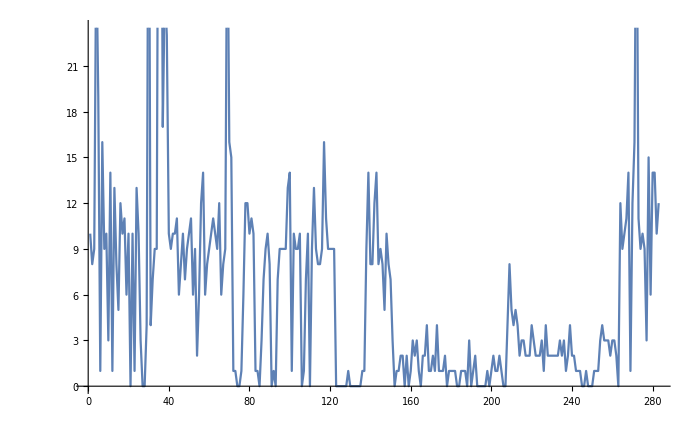

```mathematica
ListPlot[BinCounts[voltageTimes,{0,Max[voltageTimes],4 60}],Joined->True]
```